```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Solving for the pion γ and β in terms of kinetic energy of pion Eπ (arbitrary parameter but of order ~ 500 MeV)

```mathematica
Solve[(γ-1)mπ==Eπ/.γ->1/Sqrt[1-β^2],β]//Simplify
```

{{β→-(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)},{β→(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)}}

#### Define Emax (in the simplest approximation)

```mathematica
Emax:=((2me*β^2 γ^2)/.{γ->1/Sqrt[1-β^2]})/.β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)
```

```mathematica
Emax//FullSimplify
```

(2 Eπ me (Eπ+2 mπ))/mπ^2

```mathematica
dσdE=2Pi*(α^2 Z^2)/(me*β^2*Ed^2)(1-β^2 Ed/emax)//FullSimplify;
```

```mathematica
dEdx=Integrate[dσdE*n*Ed,Ed]//FullSimplify
```

(2 n π Z^2 α^2 (-(Ed β^2)/emax+Log[Ed]))/(me β^2)

```mathematica
(dEdx/.Ed->emax)-(dEdx/.Ed->emin)
```

(2 n π Z^2 α^2 (-β^2+Log[emax]))/(me β^2)-(2 n π Z^2 α^2 (-(emin β^2)/emax+Log[emin]))/(me β^2)

```mathematica
stoppingpower=2Pi*(n*Z^2*α^2)/(me*β^2)(Log[Emax/emin]-β^2)/.β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)//FullSimplify;
```

#### Express number density in units of MeV

```mathematica
Convert[10^33/Centimeter^3*(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]//N
```

8. ElectronVolt^3 Mega^3

#### Plot of stopping power, with numerics

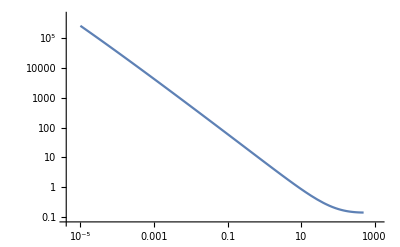

```mathematica
LogLogPlot[stoppingpower/.{n->8,me->0.511,emin->10^-10,α->1/137,mπ->139.57,Z->1},{Eπ,0.00001,500}]
```

#### Comparing with the PDG, which measures dE/dx in MeV g^-1 cm^2 for differing materials (normalized by density) and finds O(1) values:

```mathematica
Convert[0.15(Mega ElectronVolt)^2*( (5*10^9 Gram)/Centimeter^3)^-1*1/(200 Mega ElectronVolt*Fermi),(Mega ElectronVolt*Centimeter^2/Gram)]
```

(1.5 Centimeter^2 ElectronVolt Mega)/Gram

#### Range for a typical value of Eπ (with n varying over densities)

```mathematica
Table[Convert[(NIntegrate[stoppingpower^-1/.{me->0.511,emin->10^-20,α->1/137,mπ->139.57,Z->1},{Eπ,0,500}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{n,{0.008,0.08,0.8,8}}]
```

{0.0000316534 Centimeter,3.16534×10^-6 Centimeter,3.16534×10^-7 Centimeter,3.16534×10^-8 Centimeter}

```mathematica
PDGmax=Integrate[dσdE*n*Ed,{Ed,emin,Min[2me*γ^2*α^2,emax]}]/.{emax->Emax}/.{γ->1/Sqrt[1-β^2]}/.{β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)}/.{me->0.511,α->1/137,mπ->139.57,Z->1,emin->10^-20}//Simplify;
```

```mathematica
Table[Convert[NIntegrate[PDGmax^-1,{Eπ,0,500}]/(Mega ElectronVolt)(200 Mega ElectronVolt*Fermi),Centimeter],{n,{0.008,0.08,0.8,8}}]
```

{0.0000389243 Centimeter,3.89243×10^-6 Centimeter,3.89243×10^-7 Centimeter,3.89243×10^-8 Centimeter}

#### Plot R for varying values of Eπ

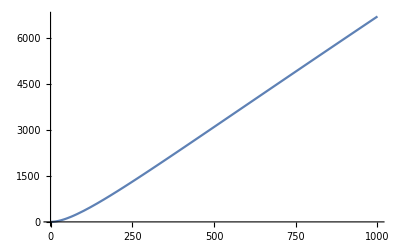

```mathematica
Plot[NIntegrate[stoppingpower^-1/.{n->8,me->0.511,emin->10^-10,α->1/137,mπ->139.57,Z->1},{Eπ,0,d}],{d,0,1000}]
```

#### In terms of PDG units, which gives range (normalized by density) of order O(1000 gm cm^-2):

```mathematica
Convert[3000/(Mega ElectronVolt)*( (5*10^9 Gram)/Centimeter^3)*(200 Mega ElectronVolt*Fermi),Gram/Centimeter^2]
```

(300 Gram)/Centimeter^2

#### Now incorporate Pauli-Blocking.

#### For relativistic fermi gas:

```mathematica
npaulirel:=Integrate[e^2/Pi^2,{e,Ef-Ed,Ef}]
```

```mathematica
npaulirel
```

Ed^3/(3 π^2)-(Ed^2 Ef)/π^2+(Ed Ef^2)/π^2

```mathematica
npaulirel/.{Ed->Ef}
```

Ef^3/(3 π^2)

```mathematica
(3 Pi^2 n)^(1/3)/.n->8//N
```

6.18734

```mathematica
plotrel=Plot[npaulirel/.{Ef->2 3^(1/3) π^(2/3),n->8},{Ed,0,2 3^(1/3) π^(2/3)}];
```

#### Using naive pauliblocking factor (Ed/Ef), where Ed is deposited energy

```mathematica
naiveplotrel=Plot[n*(Ed/Ef)/.{Ef->2 3^(1/3) π^(2/3),n->8},{Ed,0,2 3^(1/3) π^(2/3)}];
```

#### Comparing “effective” number density available for depositing energy Ed, with upper end of plot being Fermi energy.

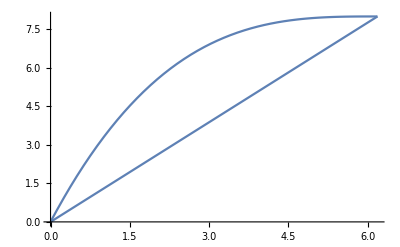

```mathematica
Show[plotrel,naiveplotrel]
```

```mathematica
dσdE
```

(2 π Z^2 α^2 (1-(Ed β^2)/emax))/(Ed^2 me β^2)

```mathematica
npaulirel
```

Ed^3/(3 π^2)-(Ed^2 Ef)/π^2+(Ed Ef^2)/π^2

```mathematica
dedxrel:=Integrate[dσdE*npaulirel*Ed,{Ed,0,Min[Ef,emax]}]//Expand
```

```mathematica
dedxnaive:=Integrate[dσdE*n(Ed/Ef)*Ed,{Ed,0,Min[Ef,emax]}]//Expand
```

```mathematica
dedxrel
```

(2 Ef^2 Z^2 α^2 Min[Ef,emax])/(me π β^2)-(Ef^2 Z^2 α^2 Min[Ef,emax]^2)/(emax me π)-(Ef Z^2 α^2 Min[Ef,emax]^2)/(me π β^2)+(2 Ef Z^2 α^2 Min[Ef,emax]^3)/(3 emax me π)+(2 Z^2 α^2 Min[Ef,emax]^3)/(9 me π β^2)-(Z^2 α^2 Min[Ef,emax]^4)/(6 emax me π)

```mathematica
dedxnaive
```

(2 n π Z^2 α^2 Min[Ef,emax])/(Ef me β^2)-(n π Z^2 α^2 Min[Ef,emax]^2)/(Ef emax me)

```mathematica
dedxnorm:=(Integrate[dσdE*n*Ed,Ed]/.Ed->Max[Ef,emax])-(Integrate[dσdE*n*Ed,Ed]/.Ed->Ef)//Expand
```

```mathematica
dedxnorm
```

(2 Ef n π Z^2 α^2)/(emax me)-(2 n π Z^2 α^2 Log[Ef])/(me β^2)+(2 n π Z^2 α^2 Log[Max[Ef,emax]])/(me β^2)-(2 n π Z^2 α^2 Max[Ef,emax])/(emax me)

```mathematica
dedxpauli:=((dedxrel+dedxnorm/.{emax->Emax,Ef->(3 Pi^2 n)^(1/3)})/.β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ))/.{me->0.511,α->1/137,mπ->139.57,Z->1}
```

```mathematica
dedxpaulinaive:=((dedxnaive+dedxnorm/.{emax->Emax,Ef->(3 Pi^2 n)^(1/3)})/.β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ))/.{me->0.511,α->1/137,mπ->139.57,Z->1}
```

```mathematica
Table[Convert[NIntegrate[dedxpauli^-1,{Eπ,0,500}]/(Mega ElectronVolt)(200 Mega ElectronVolt*Fermi),Centimeter],{n,{0.008,0.08,0.8,8}}]//N
```

{0.000473582 Centimeter,0.0000640821 Centimeter,9.57599×10^-6 Centimeter,1.60798×10^-6 Centimeter}

```mathematica
Table[Convert[NIntegrate[dedxpaulinaive^-1,{Eπ,0,500}]/(Mega ElectronVolt)(200 Mega ElectronVolt*Fermi),Centimeter],{n,{0.008,0.08,0.8,8}}]//N
```

{0.000675689 Centimeter,0.000105326 Centimeter,0.0000187976 Centimeter,3.74582×10^-6 Centimeter}

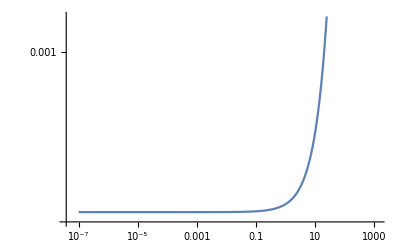

```mathematica
LogLogPlot[dedxpaulinaive/.n->8,{Eπ,0.0000001,500}]
```

```mathematica
paulimax=Integrate[dσdE*npaulirel*Ed,{Ed,emin,Min[2me*γ^2*α^2,emax]}]/.{emax->Emax,Ef->(3 Pi^2 n)^(1/3)}/.{γ->1/Sqrt[1-β^2]}/.{β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)}/.{me->0.511,α->1/137,mπ->139.57,Z->1,emin->10^-20}//Simplify;
```

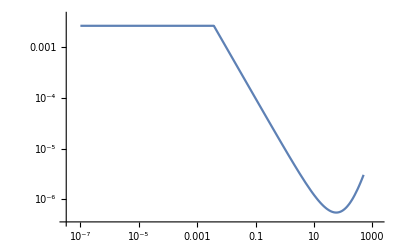

```mathematica
LogLogPlot[paulimax/.n->8,{Eπ,0.0000001,500}]
```

```mathematica
Table[Convert[NIntegrate[paulimax^-1,{Eπ,0,500}]/(Mega ElectronVolt)(200 Mega ElectronVolt*Fermi),Centimeter],{n,{0.008,0.08,0.8,8}}]
```

{0.911937 Centimeter,0.196442 Centimeter,0.0423193 Centimeter,0.00911714 Centimeter}

```mathematica
paulimaxnaive=Integrate[dσdE*n(Ed/Ef)*Ed,{Ed,emin,Min[2me*γ^2*α^2,emax]}]/.{emax->Emax,Ef->(3 Pi^2 n)^(1/3)}/.{γ->1/Sqrt[1-β^2]}/.{β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)}/.{me->0.511,α->1/137,mπ->139.57,Z->1,emin->10^-20}//Simplify;
```

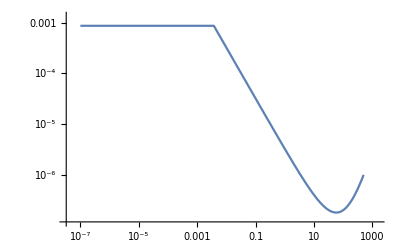

```mathematica
LogLogPlot[paulimaxnaive/.n->8,{Eπ,0.0000001,500}]
```

```mathematica
Table[Convert[NIntegrate[paulimaxnaive^-1,{Eπ,0,500}]/(Mega ElectronVolt)(200 Mega ElectronVolt*Fermi),Centimeter],{n,{0.008,0.08,0.8,8}}]
```

{2.73507 Centimeter,0.589252 Centimeter,0.126951 Centimeter,0.0273507 Centimeter}